-Graphics3D-

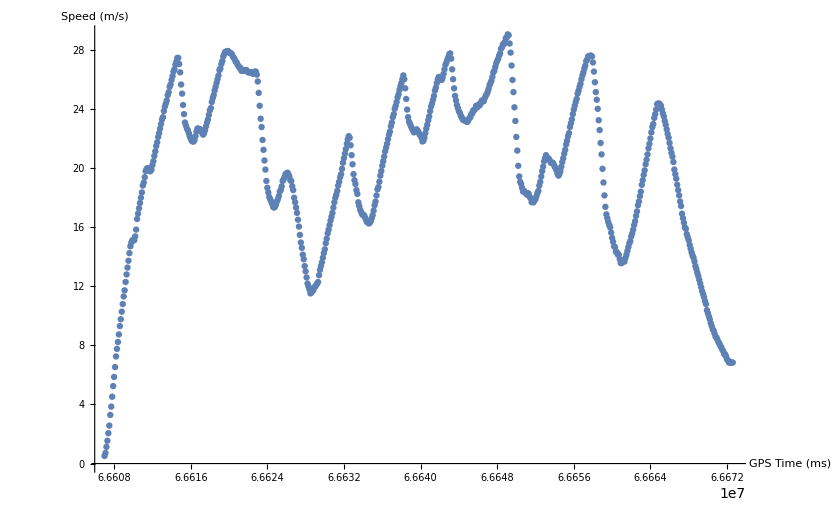

```mathematica
data=Import["C:\\Users\\BTx01\\Downloads\\scca l 7_22_18-ken-4.csv","Data"];
TableForm[data];
longlatelev=data[[2;;,2;;4]];
timespeed=data[[2;;,{1,5}]];
ListPointPlot3D[longlatelev,AxesLabel->{"Longitude (°)","Latitude (°)","Elevation (m)"},Filling->Bottom, ColorFunction->"Rainbow",PlotStyle->PointSize[Medium]]
ListPlot[timespeed,AxesLabel->{"GPS Time (ms)","Speed (m/s)"}]
```